# Linear Stability Analysis Fast Modes

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/lei/code/fast-modes-due2m

```mathematica
rMatrix[alpha_]:=1/2{
{1,-alpha,1,-alpha},
{1,alpha,1,alpha},
{1,-alpha,-1,alpha},
{1,alpha,-1,-alpha}
};
```

```mathematica
rMatrix2={
{1,0,1,0},
{0,1,0,1},
{-1,0,1,0},
{0,-1,0,1}
}
```

{{1,0,1,0},{0,1,0,1},{-1,0,1,0},{0,-1,0,1}}

```mathematica
rMatrix[a]//FullSimplify//MatrixForm
Inverse@rMatrix[a]//FullSimplify//MatrixForm
rMatrix[a].Inverse@rMatrix[a]
```

(1/2 | -a/2 | 1/2 | -a/2
1/2 | a/2 | 1/2 | a/2
1/2 | -a/2 | -1/2 | a/2
1/2 | a/2 | -1/2 | -a/2)

(1/2 | 1/2 | 1/2 | 1/2
-1/(2 a) | 1/(2 a) | -1/(2 a) | 1/(2 a)
1/2 | 1/2 | -1/2 | -1/2
-1/(2 a) | 1/(2 a) | 1/(2 a) | -1/(2 a))

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
rMatrix[alpha].{deltaL,deltaLB,deltaR,deltaRB}//FullSimplify//MatrixForm
```

(1/2 (deltaL+deltaR-alpha (deltaLB+deltaRB))
1/2 (deltaL+deltaR+alpha (deltaLB+deltaRB))
1/2 (deltaL-deltaR+alpha (-deltaLB+deltaRB))
1/2 (deltaL-deltaR+alpha (deltaLB-deltaRB)))

## Autogenerate Matrices

```mathematica
rhoL={{1,deltaL},{Conjugate@deltaL,0}};
rhoLB={{1,deltaLB},{Conjugate@deltaLB,0}};
rhoR={{1,deltaR},{Conjugate@deltaR,0}};
rhoRB={{1,deltaRB},{Conjugate@deltaRB,0}};
```

```mathematica
{{a,b},{Conjugate@b,d}}.rhoL-rhoL.{{a,b},{Conjugate@b,d}}//FullSimplify//MatrixForm
```

(-deltaL Conjugate[b]+b Conjugate[deltaL] | -b+(a-d) deltaL
Conjugate[b]+(-a+d) Conjugate[deltaL] | deltaL Conjugate[b]-b Conjugate[deltaL])

```mathematica
hnuL[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=1/2(lambda-eta omegav)PauliMatrix[3]-alpha mu (1-Cos[theta1-theta2])rhoLB-alpha mu(1+Cos[theta1+theta2])rhoRB+mu(1+Cos[2theta1])rhoR
hnuLB[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=1/2(lambda+eta omegav)PauliMatrix[3]+mu(1-Cos[theta1-theta2])rhoL-alpha mu (1+Cos[2theta2])rhoRB+mu(1+Cos[theta1+theta2])rhoR
hnuRB[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=1/2(lambda+eta omegav)PauliMatrix[3]+mu(1+Cos[theta1+theta2])rhoL-alpha mu(1+Cos[2theta2])rhoLB+mu(1-Cos[theta1-theta2])rhoR
hnuR[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=1/2(lambda-eta omegav)PauliMatrix[3]+mu(1+Cos[2theta1])rhoL-alpha mu(1+Cos[theta1+theta2])rhoLB-alpha mu(1-Cos[theta1-theta2])rhoRB
```

```mathematica
rhsL[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=hnuL[eta,mk,mu,alpha,theta1,theta2,lambda,omegav].rhoL-rhoL.hnuL[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]//FullSimplify
rhsLB[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=hnuLB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav].rhoLB-rhoLB.hnuLB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]//FullSimplify
rhsRB[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=hnuRB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav].rhoRB-rhoRB.hnuRB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]//FullSimplify
rhsR[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=hnuR[eta,mk,mu,alpha,theta1,theta2,lambda,omegav].rhoR-rhoR.hnuR[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]//FullSimplify
```

```mathematica
coefL[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=Table[
Coefficient[
rhsL[eta,mk,mu,alpha,theta1,theta2,lambda,omegav][[1,2]],
variable
],
{variable,{deltaL,deltaLB,deltaR,deltaRB}}]

coefLB[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=Table[
Coefficient[
rhsLB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav][[1,2]],
variable
],
{variable,{deltaL,deltaLB,deltaR,deltaRB}}]

coefR[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=Table[
Coefficient[
rhsR[eta,mk,mu,alpha,theta1,theta2,lambda,omegav][[1,2]],
variable
],
{variable,{deltaL,deltaLB,deltaR,deltaRB}}]

coefRB[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:=Table[
Coefficient[
rhsRB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav][[1,2]],
variable
],
{variable,{deltaL,deltaLB,deltaR,deltaRB}}]
```

```mathematica
coefMatrix[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_]:={
coefL[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]/Sin[theta1]+mk Cot[theta1]{1,0,0,0},
coefLB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]/Sin[theta2]+mk Cot[theta2]{0,1,0,0},
coefR[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]/Sin[theta1]-mk Cot[theta1]{0,0,1,0},
coefRB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]/Sin[theta2]-mk Cot[theta2]{0,0,0,1}
}
```

```mathematica
coefMatrix[eta,mk,mu,alpha,theta1,theta1,0,omegav]//MatrixForm
rMatrix[alpha].coefMatrix[eta,mk,mu,alpha,theta1,theta1,lambda,omegav].Inverse@rMatrix[alpha]//FullSimplify//MatrixForm
```

(mk Cot[theta1]+(mu-alpha mu-eta omegav+mu Cos[2 theta1]-alpha mu Cos[2 theta1]) Csc[theta1] | 0 | (-mu-mu Cos[2 theta1]) Csc[theta1] | (alpha mu+alpha mu Cos[2 theta1]) Csc[theta1]
0 | mk Cot[theta1]+(mu-alpha mu+eta omegav+mu Cos[2 theta1]-alpha mu Cos[2 theta1]) Csc[theta1] | (-mu-mu Cos[2 theta1]) Csc[theta1] | (alpha mu+alpha mu Cos[2 theta1]) Csc[theta1]
(-mu-mu Cos[2 theta1]) Csc[theta1] | (alpha mu+alpha mu Cos[2 theta1]) Csc[theta1] | -mk Cot[theta1]+(mu-alpha mu-eta omegav+mu Cos[2 theta1]-alpha mu Cos[2 theta1]) Csc[theta1] | 0
(-mu-mu Cos[2 theta1]) Csc[theta1] | (alpha mu+alpha mu Cos[2 theta1]) Csc[theta1] | 0 | -mk Cot[theta1]+(mu-alpha mu+eta omegav+mu Cos[2 theta1]-alpha mu Cos[2 theta1]) Csc[theta1])

(lambda Csc[theta1] | -eta omegav Csc[theta1] | mk Cot[theta1] | 0
-(mu+alpha mu+eta omegav+(1+alpha) mu Cos[2 theta1]) Csc[theta1] | (lambda+mu-alpha mu-(-1+alpha) mu Cos[2 theta1]) Csc[theta1] | 0 | mk Cot[theta1]
mk Cot[theta1] | 0 | (lambda-4 (-1+alpha) mu) Csc[theta1]+4 (-1+alpha) mu Sin[theta1] | -eta omegav Csc[theta1]
0 | mk Cot[theta1] | (mu+alpha mu-eta omegav+(1+alpha) mu Cos[2 theta1]) Csc[theta1] | (lambda+mu-alpha mu-(-1+alpha) mu Cos[2 theta1]) Csc[theta1])

```mathematica
coefL[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]
```

{lambda+mu-2 alpha mu-eta omegav+mu Cos[2 theta1]+2 alpha mu Sin[theta1] Sin[theta2],alpha mu-alpha mu Cos[theta1-theta2],-mu-mu Cos[2 theta1],alpha mu+alpha mu Cos[theta1+theta2]}

```mathematica
coefLB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]
```

{-mu+mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],lambda+2 mu-alpha mu+eta omegav-alpha mu Cos[2 theta2]-2 mu Sin[theta1] Sin[theta2],-mu-mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],alpha mu+alpha mu Cos[2 theta2]}

```mathematica
coefR[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]
```

{-mu-mu Cos[2 theta1],alpha mu+alpha mu Cos[theta1] Cos[theta2]-alpha mu Sin[theta1] Sin[theta2],lambda+mu-2 alpha mu-eta omegav+mu Cos[2 theta1]+2 alpha mu Sin[theta1] Sin[theta2],alpha mu-alpha mu Cos[theta1] Cos[theta2]-alpha mu Sin[theta1] Sin[theta2]}

```mathematica
coefRB[eta,mk,mu,alpha,theta1,theta2,lambda,omegav]
```

{-mu-mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],alpha mu+alpha mu Cos[2 theta2],-mu+mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],lambda+2 mu-alpha mu+eta omegav-alpha mu Cos[2 theta2]-2 mu Sin[theta1] Sin[theta2]}

```mathematica
transMatrix[eta,mk,mu,alpha,theta1,theta2,lambda,omegav][[2,1]]//FullSimplify
({-mu+mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],lambda+2 mu-alpha mu+eta omegav-alpha mu Cos[2 theta2]-2 mu Sin[theta1] Sin[theta2],-mu-mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],alpha mu+alpha mu Cos[2 theta2]}/Sin[theta2]+mk Cot[theta2]{0,1,0,0})[[1]]//FullSimplify
```

alpha mu (-1+Cos[theta1-theta2]) Csc[theta2]

mu (Cos[theta1] Cot[theta2]-Csc[theta2]+Sin[theta1])

## Equations

```mathematica
deltaVector[z_]:={deltaL[z],deltaLB[z],deltaR[z],deltaRB[z]};
```

```mathematica
transMatrix[eta_,mk_,mu_,alpha_,theta1_,theta2_,lambda_,omegav_:0]:=Module[{},

(* theta1 for neutrinos, theta2 for antineutrinos *)

{
{lambda+mu-2 alpha mu-eta omegav+mu Cos[2 theta1]+2 alpha mu Sin[theta1] Sin[theta2],alpha mu-alpha mu Cos[theta1-theta2],-mu-mu Cos[2 theta1],alpha mu+alpha mu Cos[theta1+theta2]}/Sin[theta1]+mk Cot[theta1]{1,0,0,0},
{-mu+mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],lambda+2 mu-alpha mu+eta omegav-alpha mu Cos[2 theta2]-2 mu Sin[theta1] Sin[theta2],-mu-mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],alpha mu+alpha mu Cos[2 theta2]}/Sin[theta2]+mk Cot[theta2]{0,1,0,0},
{-mu-mu Cos[2 theta1],alpha mu+alpha mu Cos[theta1] Cos[theta2]-alpha mu Sin[theta1] Sin[theta2],lambda+mu-2 alpha mu-eta omegav+mu Cos[2 theta1]+2 alpha mu Sin[theta1] Sin[theta2],alpha mu-alpha mu Cos[theta1] Cos[theta2]-alpha mu Sin[theta1] Sin[theta2]}/Sin[theta1]-mk Cot[theta1]{0,0,1,0},
{-mu-mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],alpha mu+alpha mu Cos[2 theta2],-mu+mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2],lambda+2 mu-alpha mu+eta omegav-alpha mu Cos[2 theta2]-2 mu Sin[theta1] Sin[theta2]}/Sin[theta2]-mk Cot[theta2]{0,0,0,1}
}

(*{
mk Cos[theta1]+lambda-eta omegav+mu(1+Cos[2theta1])-alpha mu(1-Cos[theta1-theta2])-alpha mu(1+Cos[theta1+theta2]),
alpha mu(1-Cos[theta1-theta2]),
- mu (1+Cos[2theta1]),
alpha mu(1+Cos[theta1+theta2])
}/Sin[theta1],
{
-alpha mu(1-Cos[theta1-theta2]),
mk Cos[theta2]+lambda+eta omegav+alpha mu(1-Cos[theta1-theta2])-alpha mu(1+Cos[2theta2])+mu(1+Cos[theta1+theta2]),
- mu(1+Cos[theta1+theta2]),
alpha mu(1+Cos[2theta2])
}/Sin[theta2],
{
-mu(1+Cos[2theta1]),
alpha mu(1+Cos[theta1+theta2]),
-mk Cos[theta1]+lambda -eta omegav+mu(1+Cos[2theta1])-alpha mu (1-Cos[theta1-theta2])-alpha mu(1+Cos[theta1+theta2]),alpha mu(1-Cos[theta1-theta2])
}/Sin[theta1],
{
-mu(1+Cos[theta1+theta2]),
alpha mu (1+Cos[2theta2]),
- mu(1-Cos[theta1-theta2]),
-mk Cos[theta2]+lambda+eta omegav+mu(1-Cos[theta1-theta2])-alpha mu(1+Cos[2theta2])+ mu (1+Cos[theta1+theta2])
}/Sin[theta2]
}*)

]
```

Validation

## With Duan’s Paper

```mathematica
transMatrix[eta,mk,mu,alpha,theta,theta,lambda,omegav]//MatrixForm
transMatrix[eta,0,mu,alpha,theta,theta,0]//MatrixForm
```

(mk Cot[theta]+Csc[theta] (lambda+mu-2 alpha mu-eta omegav+mu Cos[2 theta]+2 alpha mu Sin[theta]^2) | 0 | (-mu-mu Cos[2 theta]) Csc[theta] | (alpha mu+alpha mu Cos[2 theta]) Csc[theta]
Csc[theta] (-mu+mu Cos[theta]^2+mu Sin[theta]^2) | mk Cot[theta]+Csc[theta] (lambda+2 mu-alpha mu+eta omegav-alpha mu Cos[2 theta]-2 mu Sin[theta]^2) | Csc[theta] (-mu-mu Cos[theta]^2+mu Sin[theta]^2) | (alpha mu+alpha mu Cos[2 theta]) Csc[theta]
(-mu-mu Cos[2 theta]) Csc[theta] | Csc[theta] (alpha mu+alpha mu Cos[theta]^2-alpha mu Sin[theta]^2) | -mk Cot[theta]+Csc[theta] (lambda+mu-2 alpha mu-eta omegav+mu Cos[2 theta]+2 alpha mu Sin[theta]^2) | Csc[theta] (alpha mu-alpha mu Cos[theta]^2-alpha mu Sin[theta]^2)
Csc[theta] (-mu-mu Cos[theta]^2+mu Sin[theta]^2) | (alpha mu+alpha mu Cos[2 theta]) Csc[theta] | Csc[theta] (-mu+mu Cos[theta]^2+mu Sin[theta]^2) | -mk Cot[theta]+Csc[theta] (lambda+2 mu-alpha mu+eta omegav-alpha mu Cos[2 theta]-2 mu Sin[theta]^2))

(Csc[theta] (mu-2 alpha mu+mu Cos[2 theta]+2 alpha mu Sin[theta]^2) | 0 | (-mu-mu Cos[2 theta]) Csc[theta] | (alpha mu+alpha mu Cos[2 theta]) Csc[theta]
Csc[theta] (-mu+mu Cos[theta]^2+mu Sin[theta]^2) | Csc[theta] (2 mu-alpha mu-alpha mu Cos[2 theta]-2 mu Sin[theta]^2) | Csc[theta] (-mu-mu Cos[theta]^2+mu Sin[theta]^2) | (alpha mu+alpha mu Cos[2 theta]) Csc[theta]
(-mu-mu Cos[2 theta]) Csc[theta] | Csc[theta] (alpha mu+alpha mu Cos[theta]^2-alpha mu Sin[theta]^2) | Csc[theta] (mu-2 alpha mu+mu Cos[2 theta]+2 alpha mu Sin[theta]^2) | Csc[theta] (alpha mu-alpha mu Cos[theta]^2-alpha mu Sin[theta]^2)
Csc[theta] (-mu-mu Cos[theta]^2+mu Sin[theta]^2) | (alpha mu+alpha mu Cos[2 theta]) Csc[theta] | Csc[theta] (-mu+mu Cos[theta]^2+mu Sin[theta]^2) | Csc[theta] (2 mu-alpha mu-alpha mu Cos[2 theta]-2 mu Sin[theta]^2))

```mathematica
rMatrix[alpha].transMatrix[eta,m,mu,alpha,theta,theta,0,omegav].Inverse[rMatrix[alpha]]//FullSimplify//MatrixForm
```

(0 | -eta omegav Csc[theta] | m Cot[theta] | 0
-(mu+alpha mu+eta omegav+(1+alpha) mu Cos[2 theta]) Csc[theta] | -2 (-1+alpha) mu Cos[theta] Cot[theta] | 0 | m Cot[theta]
m Cot[theta] | 0 | -4 (-1+alpha) mu Cos[theta] Cot[theta] | -eta omegav Csc[theta]
0 | m Cot[theta] | (mu+alpha mu-eta omegav+(1+alpha) mu Cos[2 theta]) Csc[theta] | -2 (-1+alpha) mu Cos[theta] Cot[theta])

The matrix above is exactly the same as the result from Duan. We could also check it numerically.

```mathematica
Module[{etaM,alphaM,lambdaM,muS,muE,mkS,mkE,densityM,mkListM,muListM,muStepM,mkStepM,theta1M,theta2M,pltM,transMatrixM,k0M},

etaM=1;
alphaM=0.8;
lambdaM=0;
theta1M=ArcSin[0.5];
theta2M=ArcSin[0.5];
muS=0;
muE=500/(1+Cos[2theta1M]);
mkS=0;
mkE=50;
k0M=1/10;
muStepM=1;
mkStepM=1;

(*
DensityPlot[Max[
Im@Eigenvalues[
transMatrix[1,mk,mu,alphaM,Pi/6,Pi/3,0]
]],{mk,0,10},{mu,0,10},PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues",ImageSize->600,FrameLabel->{"μ/ω_v","√(|m|)"},MaxRecursion->2,PlotPoints->100,ColorFunction->GrayLevel]
*)



densityM=Table[
Max[
Im@Eigenvalues[
transMatrix[etaM,(mk)^2*k0M,mu,alphaM,theta1M,theta2M,lambdaM,1]
]
],
{mk,mkS,mkE,mkStepM},{mu,muS,muE,muStepM}];

mkListM=Table[
{mk,mk},
{mk,mkS,mkE,mkStepM}];

mkListM=Table[
{mu,mu(1+Cos[2theta1M])},
{mu,muS,muE,muStepM}];

pltM=ListDensityPlot[densityM,PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues",ImageSize->600,FrameLabel->{"μ","mk"},ColorFunction->GrayLevel,FrameTicks->{mkListM[[;;;;50]],Automatic}];

transMatrixM=transMatrix[etaM,mk,mu,alphaM,theta1M,theta2M,lambdaM]//MatrixForm;

pltM


]
```

-Graphics-

```mathematica
Det@transMatrix[eta,mk,mu,alpha,theta,theta,lambda,omegav]//FullSimplify
```

mk^4-2 (-1+alpha) mk^2 mu (-4 lambda+5 (-1+alpha) mu)+4 mu^2 (5 (-1+alpha)^2 lambda (lambda-2 (-1+alpha) mu)+2 (-1+alpha^2) eta (lambda-5 (-1+alpha) mu) omegav+(-3+(2-3 alpha) alpha) eta^2 omegav^2)+(lambda^4-4 (-1+alpha) lambda^3 mu+8 (-1+alpha)^3 lambda mu^3+8 (-1+alpha)^2 (1+alpha) eta mu^3 omegav+4 (-1+alpha) eta^2 lambda mu omegav^2+eta^4 omegav^4+mk^2 (2 (-1+alpha)^2 mu^2-eta^2 omegav^2)-lambda^2 (mk^2+2 eta^2 omegav^2)) Csc[theta]^4+Cos[2 theta] (-2 (-1+alpha)^2 mu^2 (mk^2+4 mu ((-1+alpha) lambda+(1+alpha) eta omegav))-(-mk^4+4 (-1+alpha) lambda^3 mu+lambda^2 (mk^2-20 (-1+alpha)^2 mu^2)+4 eta mu^2 omegav (6 (-1+alpha)^2 (1+alpha) mu+(3+alpha (-2+3 alpha)) eta omegav)+mk^2 (6 (-1+alpha)^2 mu^2+eta^2 omegav^2)-4 (-1+alpha) lambda mu (2 mk^2-6 (-1+alpha)^2 mu^2+2 (1+alpha) eta mu omegav+eta^2 omegav^2)) Csc[theta]^4)

## Compare with Sajad’s Equations

First of all it should be diagonalized with rMatrix2, when m=0.

```mathematica
transMatrix[eta,m,mu,alpha,theta1,theta2,0,0]//MatrixForm
```

(m Cot[theta1]+Csc[theta1] (mu-2 alpha mu+mu Cos[2 theta1]+2 alpha mu Sin[theta1] Sin[theta2]) | (alpha mu-alpha mu Cos[theta1-theta2]) Csc[theta1] | (-mu-mu Cos[2 theta1]) Csc[theta1] | (alpha mu+alpha mu Cos[theta1+theta2]) Csc[theta1]
Csc[theta2] (-mu+mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2]) | m Cot[theta2]+Csc[theta2] (2 mu-alpha mu-alpha mu Cos[2 theta2]-2 mu Sin[theta1] Sin[theta2]) | Csc[theta2] (-mu-mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2]) | (alpha mu+alpha mu Cos[2 theta2]) Csc[theta2]
(-mu-mu Cos[2 theta1]) Csc[theta1] | Csc[theta1] (alpha mu+alpha mu Cos[theta1] Cos[theta2]-alpha mu Sin[theta1] Sin[theta2]) | -m Cot[theta1]+Csc[theta1] (mu-2 alpha mu+mu Cos[2 theta1]+2 alpha mu Sin[theta1] Sin[theta2]) | Csc[theta1] (alpha mu-alpha mu Cos[theta1] Cos[theta2]-alpha mu Sin[theta1] Sin[theta2])
Csc[theta2] (-mu-mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2]) | (alpha mu+alpha mu Cos[2 theta2]) Csc[theta2] | Csc[theta2] (-mu+mu Cos[theta1] Cos[theta2]+mu Sin[theta1] Sin[theta2]) | -m Cot[theta2]+Csc[theta2] (2 mu-alpha mu-alpha mu Cos[2 theta2]-2 mu Sin[theta1] Sin[theta2]))

```mathematica
rMatrix2.transMatrix[eta,m,mu,alpha,theta1,theta2,0,0].Inverse[rMatrix2]/.{m->0}//Simplify//MatrixForm
```

(2 alpha mu (-Csc[theta1]+Sin[theta2]) | 2 alpha mu (Csc[theta1]-Sin[theta2]) | 0 | 0
2 mu (-Csc[theta2]+Sin[theta1]) | 2 mu (Csc[theta2]-Sin[theta1]) | 0 | 0
0 | 0 | 2 mu ((1-alpha+Cos[2 theta1]) Csc[theta1]+alpha Sin[theta2]) | -2 alpha mu Cos[theta2] Cot[theta1]
0 | 0 | 2 mu Cos[theta1] Cot[theta2] | -2 mu ((-1+alpha+alpha Cos[2 theta2]) Csc[theta2]+Sin[theta1]))

```mathematica
sajadxi[theta1_,theta2_]:=1-Cos[theta1-theta2];
```

In the case I have,

```mathematica
xiplus=2-2Sin[theta1]Sin[theta2]
ximinus=-2Cos[theta1]Cos[theta2]

xiLR=1+Cos[2theta1]
xiLBRB=1+Cos[2theta2]
```

2-2 Sin[theta1] Sin[theta2]

-2 Cos[theta1] Cos[theta2]

1+Cos[2 theta1]

1+Cos[2 theta2]

```mathematica
sajadTransMatrix=2{
{-alpha mu xiplus/2+mu xiLR ,alpha mu ximinus/2}/Sin[theta1],
{-mu ximinus/2Sin[theta2],mu xiplus/2-alpha mu xiLBRB}/Sin[theta2]
};
sajadTransMatrix//MatrixForm//FullSimplify
```

(2 mu ((1-alpha+Cos[2 theta1]) Csc[theta1]+alpha Sin[theta2]) | -2 alpha mu Cos[theta2] Cot[theta1]
2 mu Cos[theta1] Cos[theta2] | -2 mu ((-1+alpha+alpha Cos[2 theta2]) Csc[theta2]+Sin[theta1]))

## Calculation of Fast Modes

```mathematica
pltSpecificValues[alpha_,theta1_,theta2_]:=Module[{etaM,alphaM,lambdaM,muS,muE,mkS,mkE,densityM,mkListM,muListM,muStepM,mkStepM,theta1M,theta2M,pltM,dataM,transMatrixM},

etaM=-1;
alphaM=alpha;
lambdaM=0;
muS=0;
muE=100;
mkS=0;
mkE=50;
muStepM=1;
mkStepM=1;
theta1M=theta1;
theta2M=theta2;

(*
DensityPlot[Max[
Im@Eigenvalues[
transMatrix[1,mk,mu,alphaM,Pi/6,Pi/3,0]
]],{mk,0,10},{mu,0,10},PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues",ImageSize->600,FrameLabel->{"μ/ω_v","√(|m|)"},MaxRecursion->2,PlotPoints->100,ColorFunction->GrayLevel]
*)



dataM=Table[{mu,

Im@Eigenvalues[
transMatrix[etaM,5,mu,alphaM,theta1M,theta2M,lambdaM,0]
][[2]]

},
{mu,muS,muE,muStepM}];

transMatrixM=transMatrix[etaM,0,mu,alphaM,theta1M,theta2M,lambdaM]//MatrixForm;


pltM=ListPlot[dataM,PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues\n"<>"α="<>ToString[alphaM]<>"; {θ_1,θ_2}="<>ToString[TraditionalForm@{theta1M,theta2M}],ImageSize->600,FrameLabel->{"μ","κ"},Frame->True];

pltM



]
```

```mathematica
plt1=Module[{etaM,alphaM,lambdaM,muS,muE,mkS,mkE,densityM,mkListM,muListM,muStepM,mkStepM,theta1M,theta2M,pltM,transMatrixM},

etaM=-1;
alphaM=0.7;
lambdaM=0;
muS=0;
muE=100;
mkS=0;
mkE=100;
muStepM=1;
mkStepM=1;
theta1M=1.167197;
theta2M=0.927197;

(*
DensityPlot[Max[
Im@Eigenvalues[
transMatrix[1,mk,mu,alphaM,Pi/6,Pi/3,0]
]],{mk,0,10},{mu,0,10},PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues",ImageSize->600,FrameLabel->{"μ/ω_v","√(|m|)"},MaxRecursion->2,PlotPoints->100,ColorFunction->GrayLevel]
*)



densityM=Table[
Max[
Im@Eigenvalues[
transMatrix[etaM,mk,mu,alphaM,theta1M,theta2M,lambdaM]
]
],
{mk,mkS,mkE,mkStepM},{mu,muS,muE,muStepM}];

mkListM=Table[
mk,
{mk,mkS,mkE,mkStepM}];

mkListM=Table[
mu,
{mu,muS,muE,muStepM}];

pltM=ListDensityPlot[densityM,PlotLegends->Automatic,PlotLabel->"Maximum value of imaginary part of eigenvalues\n"<>"α="<>ToString[alphaM]<>"; {θ_1,θ_2}="<>ToString[TraditionalForm@{theta1M,theta2M}],ImageSize->600,FrameLabel->{"μ","mk"},ColorFunction->GrayLevel];

transMatrixM=transMatrix[etaM,mk,mu,alphaM,theta1M,theta2M,lambdaM]//MatrixForm;

pltM


]
```

-Graphics-

```mathematica
(*Export["export/fast-modes-fast-mode-no-matter-asymmetric-alpha-0.8.png",plt1]*)
```

export/fast-modes-fast-mode-no-matter-asymmetric-alpha-0.8.png

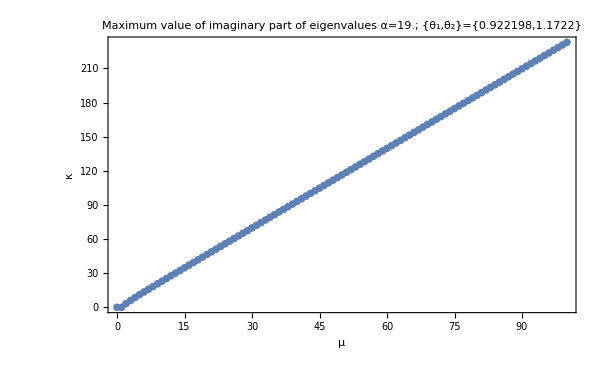

```mathematica
pltSpecificValues[(1+0.9)/(1-0.9),(2Pi/3-0.25)/2,(2Pi/3+0.25)/2]
```

Check the matrix

```mathematica
transMatrix[eta,mk,mu,alpha,theta1,theta2,0,0]//FullSimplify//MatrixForm
```

(mk Cot[theta1]+mu ((1-2 alpha+Cos[2 theta1]) Csc[theta1]+2 alpha Sin[theta2]) | -alpha mu (-1+Cos[theta1-theta2]) Csc[theta1] | -2 mu Cos[theta1] Cot[theta1] | alpha mu (1+Cos[theta1+theta2]) Csc[theta1]
mu (Cos[theta1] Cot[theta2]-Csc[theta2]+Sin[theta1]) | mk Cot[theta2]-mu (-2+alpha+alpha Cos[2 theta2]) Csc[theta2]-2 mu Sin[theta1] | -mu (Cos[theta1] Cot[theta2]+Csc[theta2]-Sin[theta1]) | 2 alpha mu Cos[theta2] Cot[theta2]
-2 mu Cos[theta1] Cot[theta1] | alpha mu (Cos[theta2] Cot[theta1]+Csc[theta1]-Sin[theta2]) | -mk Cot[theta1]+mu ((1-2 alpha+Cos[2 theta1]) Csc[theta1]+2 alpha Sin[theta2]) | -alpha mu (Cos[theta2] Cot[theta1]-Csc[theta1]+Sin[theta2])
-mu (Cos[theta1] Cot[theta2]+Csc[theta2]-Sin[theta1]) | 2 alpha mu Cos[theta2] Cot[theta2] | mu (Cos[theta1] Cot[theta2]-Csc[theta2]+Sin[theta1]) | -mk Cot[theta2]-mu (-2+alpha+alpha Cos[2 theta2]) Csc[theta2]-2 mu Sin[theta1])

```mathematica
eigenList[eta_,mkmu_,alpha_,theta1_,theta2_,lambda_:0]:=Module[{mu1M,mu2M,muM},

(*
mu1M=150;
mu2M=200;

(Eigenvalues@transMatrix[eta,mkmu*mu2M,mu2M,alpha,(sigmathetaF+deltathetaF)/2,(sigmathetaF-deltathetaF)/2,0,0]-Eigenvalues@transMatrix[eta,mkmu*mu1M,mu1M,alpha,(sigmathetaF+deltathetaF)/2,(sigmathetaF-deltathetaF)/2,0,0])/(mu2M-mu1M)
*)

Eigenvalues@transMatrix[eta,mkmu*muM,muM,alpha,theta1,theta2,lambda*muM,0]/muM

]
eigenListPM[eta_,mkmu_,alpha_,sigmathetaF_,deltathetaF_,lambda_:0]:=Module[{mu1M,mu2M,muM},

(*
mu1M=150;
mu2M=200;

(Eigenvalues@transMatrix[eta,mkmu*mu2M,mu2M,alpha,(sigmathetaF+deltathetaF)/2,(sigmathetaF-deltathetaF)/2,0,0]-Eigenvalues@transMatrix[eta,mkmu*mu1M,mu1M,alpha,(sigmathetaF+deltathetaF)/2,(sigmathetaF-deltathetaF)/2,0,0])/(mu2M-mu1M)
*)

Eigenvalues@transMatrix[eta,mkmu*muM,muM,alpha,(sigmathetaF+deltathetaF)/2,(sigmathetaF-deltathetaF)/2,lambda*muM,0]/muM

]
```

```mathematica
Max@Im@eigenList[1,0,(1-a)/(1+a),2Pi/3,-0.25]/.{a->-0.96}
```

0.

```mathematica
pltab[theta2_,mk_,export_:0,exportpath_:"export/",exportname42_:"plt.png",mustart_:150,muend_:200]:=Module[{mu1M,mu2M,eigenPltDataM,mkM,sigmathetaM,lambdaM,pltM},

mu1M=mustart;
mu2M=muend;
mkM=mk;(* in unit of mu *)
lambdaM=0;(* in unit of mu *)

(* fix theta2 *)
(*

eigenPltDataM=Flatten[
Table[{Sin[deltatheta],a,Max@Im@eigenList[1,0,(1-a)/(1+a),2Pi/3,deltatheta]},{deltatheta,-Pi/3,Pi/3,Pi/48},{a,-1,1,0.05}],
1];

ListDensityPlot[eigenPltDataM,PlotLegends->Automatic]*)

pltM=DensityPlot[Max@Im@eigenList[1,mkM,(1-a)/(1+a),(deltatheta+theta2),theta2,lambdaM],{deltatheta,-theta2,Pi/2-theta2},{a,-1,1},(*PlotRange->Full,*)(*PlotRange->{Automatic,Automatic,{0,0.5}},*)ColorFunction->GrayLevel,PlotLegends->Automatic,ImageSize->600,PlotLabel->"m k/μ="<>ToString[mkM]<>"; θ1+θ2 = "<>ToString[TraditionalForm@sigmathetaM]<>"; λ/μ="<>ToString[lambdaM],FrameLabel->{"θ_1-θ_2","a"}];

(* export=0: display image without export to image; export=1: export image without display image *)

Which[export==0,pltM,
export==1,Export[exportpath<>ToString[mk]<>"-m.png",pltM],
export==2,{pltM,
Export[exportpath<>exportname42,pltM]
}
]



]
```

```mathematica
pltab2[sigmatheta_,mk_,export_:0,exportpath_:"export/",exportname42_:"plt.png",mustart_:150,muend_:200]:=Module[{mu1M,mu2M,eigenPltDataM,mkM,sigmathetaM,lambdaM,pltM},

mu1M=mustart;
mu2M=muend;
mkM=mk;(* in unit of mu *)
lambdaM=0;(* in unit of mu *)
sigmathetaM=sigmatheta;

(* fix theta1+theta2 *)
(*

eigenPltDataM=Flatten[
Table[{Sin[deltatheta],a,Max@Im@eigenList[1,0,(1-a)/(1+a),2Pi/3,deltatheta]},{deltatheta,-Pi/3,Pi/3,Pi/48},{a,-1,1,0.05}],
1];

ListDensityPlot[eigenPltDataM,PlotLegends->Automatic]*)

pltM=DensityPlot[Max@Im@eigenListPM[1,mkM,(1-a)/(1+a),sigmathetaM,deltatheta,lambdaM],{deltatheta,-sigmathetaM,sigmathetaM},{a,-1,1},(*PlotRange->Full,*)(*PlotRange->{Automatic,Automatic,{0,0.5}},*)ColorFunction->GrayLevel,PlotLegends->Automatic,ImageSize->600,PlotLabel->"m k/μ="<>ToString[mkM]<>"; θ1+θ2 = "<>ToString[TraditionalForm@sigmathetaM]<>"; λ/μ="<>ToString[lambdaM],FrameLabel->{"θ_1-θ_2","a"}];

(* export=0: display image without export to image; export=1: export image without display image *)

Which[export==0,pltM,
export==1,Export[exportpath<>ToString[mk]<>"-m.png",pltM],
export==2,{pltM,
Export[exportpath<>exportname42,pltM]
}
]



]
```

```mathematica
pltab[0.9Pi/2,0,0]
```

-Graphics-

```mathematica
listPlt1=ParallelTable[pltab2[2Pi/3,mk,1,"export-2pi-over-3/"],
{mk,0,10,0.1}]
```

{export-2pi-over-3/0.-m.png,export-2pi-over-3/0.1-m.png,export-2pi-over-3/0.2-m.png,export-2pi-over-3/0.3-m.png,export-2pi-over-3/0.4-m.png,export-2pi-over-3/0.5-m.png,export-2pi-over-3/0.6-m.png,export-2pi-over-3/0.7-m.png,export-2pi-over-3/0.8-m.png,export-2pi-over-3/0.9-m.png,export-2pi-over-3/1.-m.png,export-2pi-over-3/1.1-m.png,export-2pi-over-3/1.2-m.png,export-2pi-over-3/1.3-m.png,export-2pi-over-3/1.4-m.png,export-2pi-over-3/1.5-m.png,export-2pi-over-3/1.6-m.png,export-2pi-over-3/1.7-m.png,export-2pi-over-3/1.8-m.png,export-2pi-over-3/1.9-m.png,export-2pi-over-3/2.-m.png,export-2pi-over-3/2.1-m.png,export-2pi-over-3/2.2-m.png,export-2pi-over-3/2.3-m.png,export-2pi-over-3/2.4-m.png,export-2pi-over-3/2.5-m.png,export-2pi-over-3/2.6-m.png,export-2pi-over-3/2.7-m.png,export-2pi-over-3/2.8-m.png,export-2pi-over-3/2.9-m.png,export-2pi-over-3/3.-m.png,export-2pi-over-3/3.1-m.png,export-2pi-over-3/3.2-m.png,export-2pi-over-3/3.3-m.png,export-2pi-over-3/3.4-m.png,export-2pi-over-3/3.5-m.png,export-2pi-over-3/3.6-m.png,export-2pi-over-3/3.7-m.png,export-2pi-over-3/3.8-m.png,export-2pi-over-3/3.9-m.png,export-2pi-over-3/4.-m.png,export-2pi-over-3/4.1-m.png,export-2pi-over-3/4.2-m.png,export-2pi-over-3/4.3-m.png,export-2pi-over-3/4.4-m.png,export-2pi-over-3/4.5-m.png,export-2pi-over-3/4.6-m.png,export-2pi-over-3/4.7-m.png,export-2pi-over-3/4.8-m.png,export-2pi-over-3/4.9-m.png,export-2pi-over-3/5.-m.png,export-2pi-over-3/5.1-m.png,export-2pi-over-3/5.2-m.png,export-2pi-over-3/5.3-m.png,export-2pi-over-3/5.4-m.png,export-2pi-over-3/5.5-m.png,export-2pi-over-3/5.6-m.png,export-2pi-over-3/5.7-m.png,export-2pi-over-3/5.8-m.png,export-2pi-over-3/5.9-m.png,export-2pi-over-3/6.-m.png,export-2pi-over-3/6.1-m.png,export-2pi-over-3/6.2-m.png,export-2pi-over-3/6.3-m.png,export-2pi-over-3/6.4-m.png,export-2pi-over-3/6.5-m.png,export-2pi-over-3/6.6-m.png,export-2pi-over-3/6.7-m.png,export-2pi-over-3/6.8-m.png,export-2pi-over-3/6.9-m.png,export-2pi-over-3/7.-m.png,export-2pi-over-3/7.1-m.png,export-2pi-over-3/7.2-m.png,export-2pi-over-3/7.3-m.png,export-2pi-over-3/7.4-m.png,export-2pi-over-3/7.5-m.png,export-2pi-over-3/7.6-m.png,export-2pi-over-3/7.7-m.png,export-2pi-over-3/7.8-m.png,export-2pi-over-3/7.9-m.png,export-2pi-over-3/8.-m.png,export-2pi-over-3/8.1-m.png,export-2pi-over-3/8.2-m.png,export-2pi-over-3/8.3-m.png,export-2pi-over-3/8.4-m.png,export-2pi-over-3/8.5-m.png,export-2pi-over-3/8.6-m.png,export-2pi-over-3/8.7-m.png,export-2pi-over-3/8.8-m.png,export-2pi-over-3/8.9-m.png,export-2pi-over-3/9.-m.png,export-2pi-over-3/9.1-m.png,export-2pi-over-3/9.2-m.png,export-2pi-over-3/9.3-m.png,export-2pi-over-3/9.4-m.png,export-2pi-over-3/9.5-m.png,export-2pi-over-3/9.6-m.png,export-2pi-over-3/9.7-m.png,export-2pi-over-3/9.8-m.png,export-2pi-over-3/9.9-m.png,export-2pi-over-3/10.-m.png}

```mathematica
listPlt=ParallelTable[pltab2[Pi/3,mk,1,"export-pi-over-3/"],
{mk,0,10,0.1}]
```

{export-pi-over-3/0.-m.png,export-pi-over-3/0.1-m.png,export-pi-over-3/0.2-m.png,export-pi-over-3/0.3-m.png,export-pi-over-3/0.4-m.png,export-pi-over-3/0.5-m.png,export-pi-over-3/0.6-m.png,export-pi-over-3/0.7-m.png,export-pi-over-3/0.8-m.png,export-pi-over-3/0.9-m.png,export-pi-over-3/1.-m.png,export-pi-over-3/1.1-m.png,export-pi-over-3/1.2-m.png,export-pi-over-3/1.3-m.png,export-pi-over-3/1.4-m.png,export-pi-over-3/1.5-m.png,export-pi-over-3/1.6-m.png,export-pi-over-3/1.7-m.png,export-pi-over-3/1.8-m.png,export-pi-over-3/1.9-m.png,export-pi-over-3/2.-m.png,export-pi-over-3/2.1-m.png,export-pi-over-3/2.2-m.png,export-pi-over-3/2.3-m.png,export-pi-over-3/2.4-m.png,export-pi-over-3/2.5-m.png,export-pi-over-3/2.6-m.png,export-pi-over-3/2.7-m.png,export-pi-over-3/2.8-m.png,export-pi-over-3/2.9-m.png,export-pi-over-3/3.-m.png,export-pi-over-3/3.1-m.png,export-pi-over-3/3.2-m.png,export-pi-over-3/3.3-m.png,export-pi-over-3/3.4-m.png,export-pi-over-3/3.5-m.png,export-pi-over-3/3.6-m.png,export-pi-over-3/3.7-m.png,export-pi-over-3/3.8-m.png,export-pi-over-3/3.9-m.png,export-pi-over-3/4.-m.png,export-pi-over-3/4.1-m.png,export-pi-over-3/4.2-m.png,export-pi-over-3/4.3-m.png,export-pi-over-3/4.4-m.png,export-pi-over-3/4.5-m.png,export-pi-over-3/4.6-m.png,export-pi-over-3/4.7-m.png,export-pi-over-3/4.8-m.png,export-pi-over-3/4.9-m.png,export-pi-over-3/5.-m.png,export-pi-over-3/5.1-m.png,export-pi-over-3/5.2-m.png,export-pi-over-3/5.3-m.png,export-pi-over-3/5.4-m.png,export-pi-over-3/5.5-m.png,export-pi-over-3/5.6-m.png,export-pi-over-3/5.7-m.png,export-pi-over-3/5.8-m.png,export-pi-over-3/5.9-m.png,export-pi-over-3/6.-m.png,export-pi-over-3/6.1-m.png,export-pi-over-3/6.2-m.png,export-pi-over-3/6.3-m.png,export-pi-over-3/6.4-m.png,export-pi-over-3/6.5-m.png,export-pi-over-3/6.6-m.png,export-pi-over-3/6.7-m.png,export-pi-over-3/6.8-m.png,export-pi-over-3/6.9-m.png,export-pi-over-3/7.-m.png,export-pi-over-3/7.1-m.png,export-pi-over-3/7.2-m.png,export-pi-over-3/7.3-m.png,export-pi-over-3/7.4-m.png,export-pi-over-3/7.5-m.png,export-pi-over-3/7.6-m.png,export-pi-over-3/7.7-m.png,export-pi-over-3/7.8-m.png,export-pi-over-3/7.9-m.png,export-pi-over-3/8.-m.png,export-pi-over-3/8.1-m.png,export-pi-over-3/8.2-m.png,export-pi-over-3/8.3-m.png,export-pi-over-3/8.4-m.png,export-pi-over-3/8.5-m.png,export-pi-over-3/8.6-m.png,export-pi-over-3/8.7-m.png,export-pi-over-3/8.8-m.png,export-pi-over-3/8.9-m.png,export-pi-over-3/9.-m.png,export-pi-over-3/9.1-m.png,export-pi-over-3/9.2-m.png,export-pi-over-3/9.3-m.png,export-pi-over-3/9.4-m.png,export-pi-over-3/9.5-m.png,export-pi-over-3/9.6-m.png,export-pi-over-3/9.7-m.png,export-pi-over-3/9.8-m.png,export-pi-over-3/9.9-m.png,export-pi-over-3/10.-m.png}

```mathematica
listPlt3=ParallelTable[pltab2[Pi/3,mk,1,"export-pi-over-2/"],
{mk,0,10,0.1}]
```

{export-pi-over-2/0.-m.png,export-pi-over-2/0.1-m.png,export-pi-over-2/0.2-m.png,export-pi-over-2/0.3-m.png,export-pi-over-2/0.4-m.png,export-pi-over-2/0.5-m.png,export-pi-over-2/0.6-m.png,export-pi-over-2/0.7-m.png,export-pi-over-2/0.8-m.png,export-pi-over-2/0.9-m.png,export-pi-over-2/1.-m.png,export-pi-over-2/1.1-m.png,export-pi-over-2/1.2-m.png,export-pi-over-2/1.3-m.png,export-pi-over-2/1.4-m.png,export-pi-over-2/1.5-m.png,export-pi-over-2/1.6-m.png,export-pi-over-2/1.7-m.png,export-pi-over-2/1.8-m.png,export-pi-over-2/1.9-m.png,export-pi-over-2/2.-m.png,export-pi-over-2/2.1-m.png,export-pi-over-2/2.2-m.png,export-pi-over-2/2.3-m.png,export-pi-over-2/2.4-m.png,export-pi-over-2/2.5-m.png,export-pi-over-2/2.6-m.png,export-pi-over-2/2.7-m.png,export-pi-over-2/2.8-m.png,export-pi-over-2/2.9-m.png,export-pi-over-2/3.-m.png,export-pi-over-2/3.1-m.png,export-pi-over-2/3.2-m.png,export-pi-over-2/3.3-m.png,export-pi-over-2/3.4-m.png,export-pi-over-2/3.5-m.png,export-pi-over-2/3.6-m.png,export-pi-over-2/3.7-m.png,export-pi-over-2/3.8-m.png,export-pi-over-2/3.9-m.png,export-pi-over-2/4.-m.png,export-pi-over-2/4.1-m.png,export-pi-over-2/4.2-m.png,export-pi-over-2/4.3-m.png,export-pi-over-2/4.4-m.png,export-pi-over-2/4.5-m.png,export-pi-over-2/4.6-m.png,export-pi-over-2/4.7-m.png,export-pi-over-2/4.8-m.png,export-pi-over-2/4.9-m.png,export-pi-over-2/5.-m.png,export-pi-over-2/5.1-m.png,export-pi-over-2/5.2-m.png,export-pi-over-2/5.3-m.png,export-pi-over-2/5.4-m.png,export-pi-over-2/5.5-m.png,export-pi-over-2/5.6-m.png,export-pi-over-2/5.7-m.png,export-pi-over-2/5.8-m.png,export-pi-over-2/5.9-m.png,export-pi-over-2/6.-m.png,export-pi-over-2/6.1-m.png,export-pi-over-2/6.2-m.png,export-pi-over-2/6.3-m.png,export-pi-over-2/6.4-m.png,export-pi-over-2/6.5-m.png,export-pi-over-2/6.6-m.png,export-pi-over-2/6.7-m.png,export-pi-over-2/6.8-m.png,export-pi-over-2/6.9-m.png,export-pi-over-2/7.-m.png,export-pi-over-2/7.1-m.png,export-pi-over-2/7.2-m.png,export-pi-over-2/7.3-m.png,export-pi-over-2/7.4-m.png,export-pi-over-2/7.5-m.png,export-pi-over-2/7.6-m.png,export-pi-over-2/7.7-m.png,export-pi-over-2/7.8-m.png,export-pi-over-2/7.9-m.png,export-pi-over-2/8.-m.png,export-pi-over-2/8.1-m.png,export-pi-over-2/8.2-m.png,export-pi-over-2/8.3-m.png,export-pi-over-2/8.4-m.png,export-pi-over-2/8.5-m.png,export-pi-over-2/8.6-m.png,export-pi-over-2/8.7-m.png,export-pi-over-2/8.8-m.png,export-pi-over-2/8.9-m.png,export-pi-over-2/9.-m.png,export-pi-over-2/9.1-m.png,export-pi-over-2/9.2-m.png,export-pi-over-2/9.3-m.png,export-pi-over-2/9.4-m.png,export-pi-over-2/9.5-m.png,export-pi-over-2/9.6-m.png,export-pi-over-2/9.7-m.png,export-pi-over-2/9.8-m.png,export-pi-over-2/9.9-m.png,export-pi-over-2/10.-m.png}

Plot agains m

```mathematica
pltam[sigmatheta_,deltatheta_]:=Module[{mu1M,mu2M,eigenPltDataM,mkM,sigmathetaM,deltathetaM,lambdaM,pltM},

mu1M=150;
mu2M=200;
(*mkM=1;*)(* in unit of mu *)
lambdaM=0;(* in unit of mu *)
sigmathetaM=sigmatheta;
deltathetaM=deltatheta;

(* fix theta1+theta2 *)
(*

eigenPltDataM=Flatten[
Table[{Sin[deltatheta],a,Max@Im@eigenList[1,0,(1-a)/(1+a),2Pi/3,deltatheta]},{deltatheta,-Pi/3,Pi/3,Pi/48},{a,-1,1,0.05}],
1];

ListDensityPlot[eigenPltDataM,PlotLegends->Automatic]*)

pltM=DensityPlot[Max@Im@eigenListPM[1,mk,(1-a)/(1+a),sigmathetaM,deltathetaM,lambdaM],{mk,0,50},{a,-1,1},(*PlotRange->Full,*)(*PlotRange->{Automatic,Automatic,{0,0.5}},*)ColorFunction->GrayLevel,PlotLegends->Automatic,ImageSize->600,PlotLabel->"θ_1-θ_2="<>ToString[deltathetaM]<>"; θ1+θ2 = "<>ToString[TraditionalForm@sigmathetaM]<>"; λ/μ="<>ToString[lambdaM],FrameLabel->{"m","a"}];

pltM
(*{pltM,

Export["export/plt2-sigmatheta-2Pi-divided-by-3"<>"-mk-divided-by-mu-"<>ToString[mkM]<>"-lambda-divided-by-mu-"<>ToString[lambdaM]<>".png",pltM]}
*)

]
```

```mathematica
Table[plt3[sigmatheta,deltatheta],{sigmatheta,,2.9Pi/3},{deltatheta}]
```

Check for some specific values

```mathematica
Table[
{theta1,theta2},
{theta1,Pi/6,Pi/3,Pi/6/3},{theta2,Pi/6,Pi/3,Pi/6/3}]//Grid
```

{π/6,π/6} | {π/6,(2 π)/9} | {π/6,(5 π)/18} | {π/6,π/3}
{(2 π)/9,π/6} | {(2 π)/9,(2 π)/9} | {(2 π)/9,(5 π)/18} | {(2 π)/9,π/3}
{(5 π)/18,π/6} | {(5 π)/18,(2 π)/9} | {(5 π)/18,(5 π)/18} | {(5 π)/18,π/3}
{π/3,π/6} | {π/3,(2 π)/9} | {π/3,(5 π)/18} | {π/3,π/3}

```mathematica
pltExp1=Table[
pltSpecificValues[0.8,theta1,theta2],
{theta1,Pi/6,Pi/3,Pi/6/3},{theta2,Pi/6,Pi/3,Pi/6/3}]//Grid
```

```mathematica
(*Export["export/fast-mode-alpha-0.8.png",pltExp1]
Export["export/fast-mode-alpha-1.2.png",pltExp2]*)
```

export/fast-mode-alpha-0.8.png

export/fast-mode-alpha-1.2.png

Analytical Analysis

```mathematica
Solve[
Det[
transMatrix[eta,mk,mu,alpha,theta1,theta2,0]-eig IdentityMatrix[4]
]==0,
eig]
```

{{eig→1},{1},1,{eig→-1/2 (-2 alpha mu Csc[theta1]+2 mu Csc[theta2]-mu Csc[theta1]^2 Csc[theta2]+5+alpha mu Csc[theta1] Csc[theta2]^2+alpha mu Cos[2 theta2] Csc[theta1] Csc[theta2]^2) Sin[theta1] Sin[theta2]+1/2 1+1/2 √1}}
 |  |  |  |

```mathematica
anCharEqn[eig_]:=Collect[
Det[
transMatrix[eta,mk,mu,alpha,theta1,theta2,0]-eig IdentityMatrix[4]
],
eig]
```

```mathematica
anCharEqnA=Coefficient[anCharEqn[eig],eig,4];
anCharEqnB=Coefficient[anCharEqn[eig],eig,3];
anCharEqnC=Coefficient[anCharEqn[eig],eig,2];
anCharEqnD=Coefficient[anCharEqn[eig],eig,1];
anCharEqnE=Coefficient[anCharEqn[eig],eig,0];
```

STOP IT. Even if I can calculate the descriminat, what then? It’s extremely complicated.

```mathematica
Discriminant[a x^4+b x^3+c x^2 + d x + e,x]
```

b^2 c^2 d^2-4 a c^3 d^2-4 b^3 d^3+18 a b c d^3-27 a^2 d^4-4 b^2 c^3 e+16 a c^4 e+18 b^3 c d e-80 a b c^2 d e-6 a b^2 d^2 e+144 a^2 c d^2 e-27 b^4 e^2+144 a b^2 c e^2-128 a^2 c^2 e^2-192 a^2 b d e^2+256 a^3 e^3